```mathematica
<<Vilcretas`
```

VilCretas está disponible.

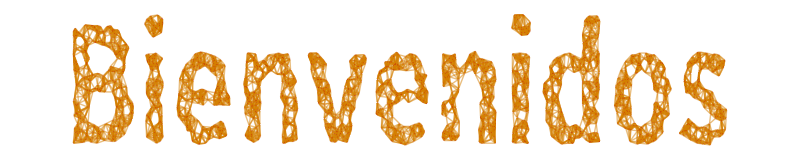

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
f = Sum[Sum[1,{j,1,(i-1)/3}],{i,1,2n-1}];
```

```mathematica
g={n, n^2,n^4,Log[n],n^3};
```

```mathematica
Table[i->Limit[f/i,n->Infinity],{i,g}]
```

{n→∞,n^2→2/3,n^4→0,Log[n]→∞,n^3→0}

```mathematica
programa1[n_,producto_:9207059489619389792649217/13456471561751415850795008]:=If[n==3,
producto,programa1[n-1,producto*
((18^(-19 (-2+n)) (1-7 18^(19 (-2+n)) (-2+n)^3+5 2^(2+19 (-2+n)) 9^(19 (-2+n)) (-2+n)^4))/(1+15 (-2+n)+3 (-2+n)^3))]]

programa2[n_]:=If[n==3,9207059489619389792649217/13456471561751415850795008,programa2[n-1]*((18^(-19 (-2+n)) (1-7 18^(19 (-2+n)) (-2+n)^3+5 2^(2+19 (-2+n)) 9^(19 (-2+n)) (-2+n)^4))/(1+15 (-2+n)+3 (-2+n)^3))]

programa3[n_]:=Product[(18^(-19 i)-7 i^3+20 i^4)/(1+15 i+3 i^3),{i,1,n-2}]
```

```mathematica
{programa1[3], programa2[3], programa3[3]}
```

{9207059489619389792649217/13456471561751415850795008,9207059489619389792649217/13456471561751415850795008,9207059489619389792649217/13456471561751415850795008}

```mathematica
PruebaADAGrafica[{programa1, programa2, programa3},10,1,3]
```

$Aborted

```mathematica
f=Sum[Sum[Sum[1,{k,1,j+3}],{j,1,i-6}],{i,1,n+5}];
```

```mathematica
Limit[f/n^4,n->Infinity]
```

0

```mathematica
f=Sum[(3 i^3+16-3)/(1-19^8),{i,2,n+1}];
```

```mathematica
g={n,n  Log[n],n^2,1,-n,-n^3,-1,-n^4};
```

```mathematica
Table[i->Limit[f/i, n->Infinity], {i,g}]
```

{n→-∞,n Log[n]→-∞,n^2→-∞,1→-∞,-n→∞,-n^3→∞,-1→∞,-n^4→1/22644750720}

```mathematica
f = n^3+(n^3+n-9160)/(6n)+9;
```

```mathematica
g=n^2;
```

```mathematica
Limit[f/g,n->Infinity]
```

∞

```mathematica
CompLimit[{f,g}]
```

∞→ (-9160+55 n+n^3+6 n^4)/(6 n)=Ω(n^2), Notación omega

```mathematica
f =n^3+(n^5+n^4-1240)/(6n)+(9(n-5))/(69-8n);
```

```mathematica
g=n^j;
```

```mathematica
CompLimit[{f,g},jvalor->100]
```

```mathematica
programa1[n_]:=Sum[(1-6 i)/(-3-19^(-5 i)),{i,2,n+2}]

programa2[n_]:=If[n==0,67441728835811/18393198773404,programa2[n-1]+((19^(5 (2+n)) (-1+6 (2+n)))/(1+3 19^(5 (2+n))))]

programa3[n_,suma_:67441728835811/18393198773404]:=If[n==0,suma,programa3[n-1,suma+((19^(5 (2+n)) (-1+6 (2+n)))/(1+3 19^(5 (2+n))))]]
```

```mathematica
{programa1[3],programa2[3], programa3[3]}
```

{10990712406865887529160168329893600496593404138503801322211275204250302962101933698228013119/412151715257473863422383191775447310702221150065746652542197271613735638425858088438089351,10990712406865887529160168329893600496593404138503801322211275204250302962101933698228013119/412151715257473863422383191775447310702221150065746652542197271613735638425858088438089351,9207059489619389792649217/13456471561751415850795008}

```mathematica
RR[{1,4},{7-2n}, k, inicio->0]
```

7+4 k-2 n